```mathematica
Get["NeutronBeam/NBeam_IntTables.m"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

General::stop: Further output of General::obspkg will be suppressed during this calculation.

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XYDatam05p75XOffset=XYDataCreation[{0.00,0.06,-0.04,7},{-0.02,0.02,0.,5}]
```

{{-0.04,-0.02},{-0.04,-0.01},{-0.04,0.},{-0.04,0.01},{-0.04,0.02},{-0.03,-0.02},{-0.03,-0.01},{-0.03,0.},{-0.03,0.01},{-0.03,0.02},{-0.02,-0.02},{-0.02,-0.01},{-0.02,0.},{-0.02,0.01},{-0.02,0.02},{-0.01,-0.02},{-0.01,-0.01},{-0.01,0.},{-0.01,0.01},{-0.01,0.02},{-6.93889×10^-18,-0.02},{-6.93889×10^-18,-0.01},{-6.93889×10^-18,0.},{-6.93889×10^-18,0.01},{-6.93889×10^-18,0.02},{0.01,-0.02},{0.01,-0.01},{0.01,0.},{0.01,0.01},{0.01,0.02},{0.02,-0.02},{0.02,-0.01},{0.02,0.},{0.02,0.01},{0.02,0.02}}

```mathematica
FitFuncTablewNbeam[b_,XYData_List,{alpha_,BRxB_,rF_,rA_,rRxB_,rD_,R_,G1_,G2_},{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]=
Int2DwNBeamCompiledManualphiAAllLimits[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
```

```mathematica
FitFuncBinwNbeam[bin_?NumericQ,b_?NumericQ,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec][[bin]]/Total[FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]]
```

### check integrand

```mathematica
ManualphiAIntegrandAllLimits[0,0.,0.0,{Pi,Pi,600000,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},True]
```

{{-3.14159,-1.39052,1.39052,-3.14159,3.14159,1.5708,1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,-1.39052,1.39052,1.5708,3.14159},{1.5708,0.180276,2.78104,0.180276,1.5708},{-2.35619,-1.48066,0.,1.48066,2.35619},{0.00022072,0.00022072,0.,0.00022072,0.00022072},0.000772993}

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

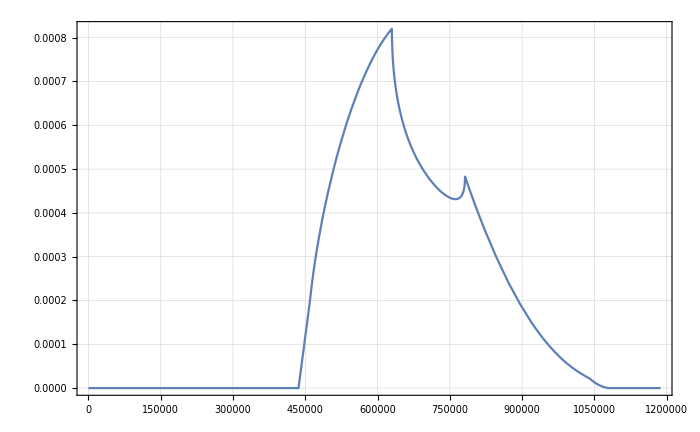

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

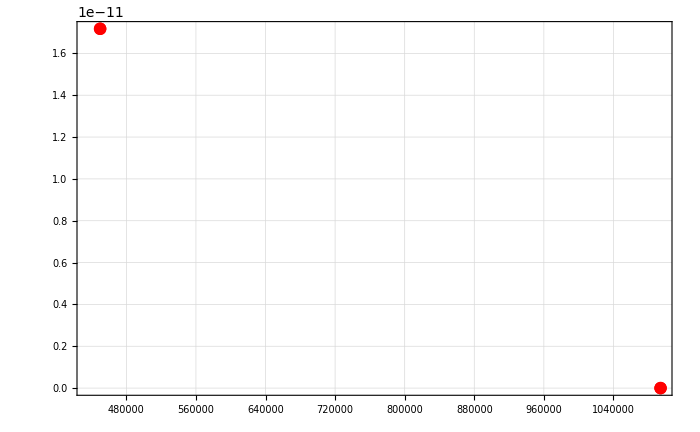

```mathematica
ListPlot[
{
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

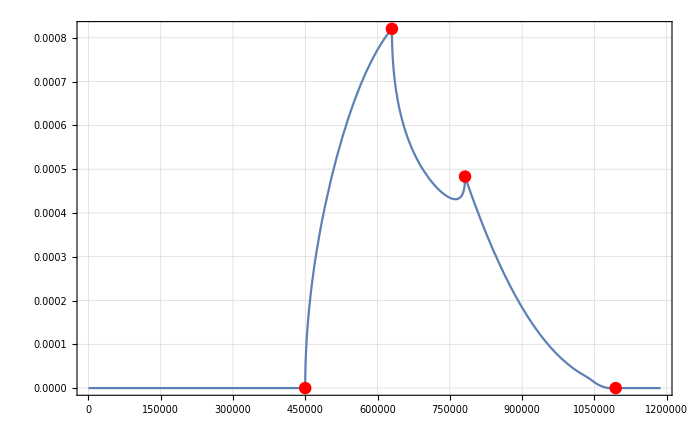

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

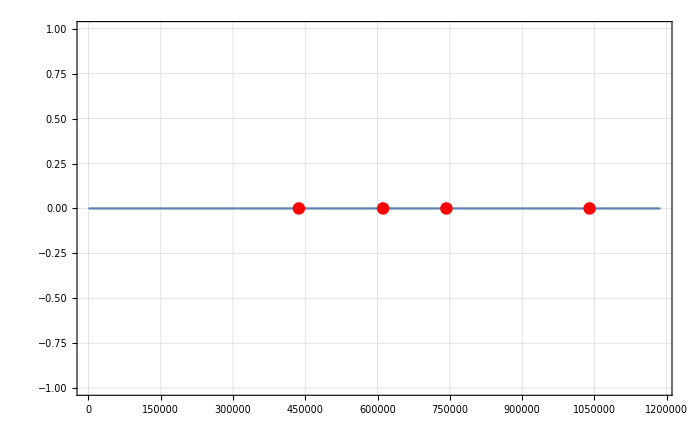

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pminApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

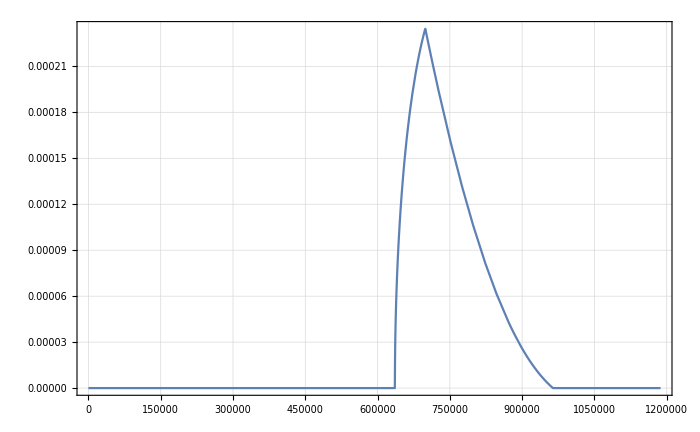

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.025,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

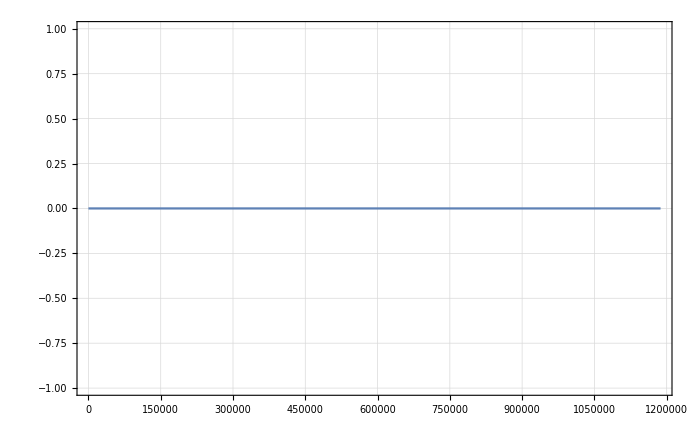

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.027,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

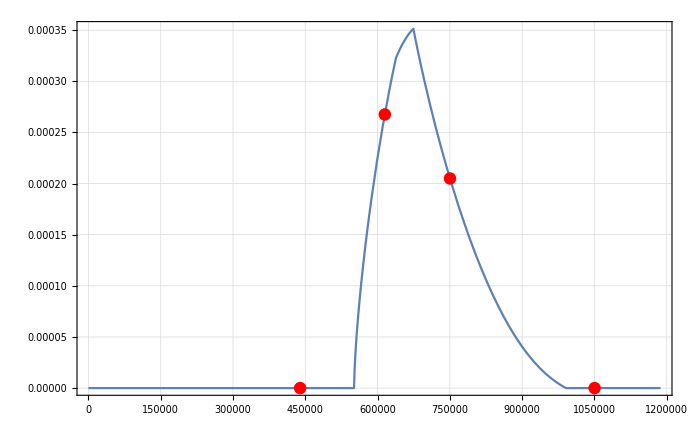

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pminApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

### here we see the y limitation, which is of course not covered by the x limitations

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 27 Feb 2020 10:13:53

{{1,0.},{2,0.00122061},{3,0.00118353},{4,0.00114943},{5,0.},{6,0.0029032},{7,0.0248097},{8,0.0240842},{9,0.0233627},{10,0.00242836},{11,0.0151144},{12,0.0645866},{13,0.0647894},{14,0.0621568},{15,0.0136134},{16,0.0242079},{17,0.0790406},{18,0.0854805},{19,0.0781183},{20,0.0232219},{21,0.0214339},{22,0.0616516},{23,0.0708215},{24,0.0628734},{25,0.0219515},{26,0.012003},{27,0.0316016},{28,0.0374659},{29,0.0336864},{30,0.0132346},{31,0.00421033},{32,0.00958779},{33,0.012112},{34,0.0108153},{35,0.00507975}}

0.928323

### 0.928h for Int2DwNBeamCompiledManualphiAAllLimits (no p intervals), 9 cores

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeam[[All,2]]}]]
```

-Graphics3D-

## Testing

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,0.0025,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},True]
```

{{-3.14159,0.,0.,-3.14159,3.14159,-1.5708,-1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,0.,3.14159},{1.5708,1.5708,3.14159},{-2.35619,-0.785398,1.5708},{0.,0.,0.},0.}

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,25,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},True]
```

{{-3.14159,0.,0.,-3.14159,3.14159,-1.5708,-1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,0.,3.14159},{1.5708,1.5708,3.14159},{-2.35619,-0.785398,1.5708},{0.,0.,0.},0.}

General::munfl: Exp[-3905.96] is too small to represent as a normalized machine number; precision may be lost.

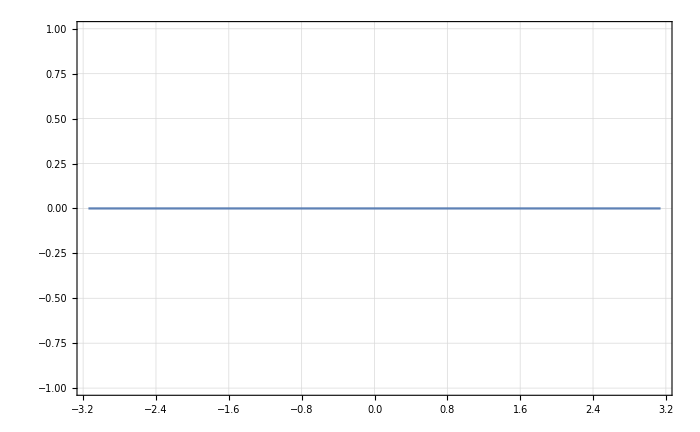

```mathematica
Plot[Integrand2DwNBeamCompiled[0.,0.0,-0.0,{-Pi/2-0.1,phiA,-Pi/2-0.1,6,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.}],{phiA,-Pi,Pi}]
```

### ok, for small p > 0, there appears to be an issue???

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,40,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False]
```

0.

```mathematica
Int2DwNBeamCompiledManualphiAAllLimitspLimitsX[0.,{{0.,0.}},{3.141592653589793,0.2,2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]
```

{3275.86}

```mathematica
CloseKernels[]
```

{KernelObject[20,193.170.93.100,<defunct>],KernelObject[22,193.170.93.100,<defunct>],KernelObject[23,193.170.93.100,<defunct>],KernelObject[24,193.170.93.100,<defunct>],KernelObject[25,local,<defunct>],KernelObject[26,local,<defunct>],KernelObject[27,local,<defunct>],KernelObject[28,local,<defunct>]}

```mathematica
LaunchKernels[4]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Fri 28 Feb 2020 14:26:12

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{-3.14159,-1.5708}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{-1.5708,0.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{0.,1.5708}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11].

Kernels::rdead: Subkernel connected through KernelObject[3,193.170.93.100] appears dead.

LinkObject::linkn: Argument LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11] in LinkClose[LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11]] has an invalid LinkObject number; the link may be closed.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{-3.14159,-1.5708}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{-1.5708,0.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{0.,1.5708}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

Part::partw: Part 10 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

Part::partw: Part 11 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

Part::partw: Part 12 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1,{0.,56.4594/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],54.7445/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],53.1672/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{2,{0.,134.288/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1147.58/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1114.02/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{3,$Failed/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{4,{2996.85/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2875.07/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],629.69/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1119.74/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{5,{3656.03/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3953.91/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3613.37/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1074.13/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{6,{991.427/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2851.71/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3275.86/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2908.22/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{7,{1015.37/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],555.199/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1461.74/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1732.99/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{8,{1558.17/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],612.17/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],194.749/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],443.485/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{9,{560.241/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],500.262/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],234.965/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{10,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦10⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{11,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦11⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{12,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦12⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{13,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦13⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{14,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦14⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{15,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦15⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{16,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦16⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{17,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦17⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{18,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦18⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{19,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦19⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{20,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦20⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{21,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦21⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{22,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦22⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{23,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦23⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{24,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦24⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{25,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦25⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{26,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦26⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{27,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦27⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{28,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦28⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{29,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦29⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{30,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦30⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{31,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦31⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{32,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦32⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{33,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦33⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{34,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦34⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{35,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦35⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}}

1.33706

```mathematica
IntegrandphiDVIntegrated[phiDet_?NumericQ,th0_?NumericQ]:=NIntegrate[ManualphiAIntegrandAllLimits[0.,0.,0.,{phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False],

{p,0.,pmax},{phiDV,-Pi//N,Pi//N},PrecisionGoal->4,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10]
```

```mathematica
Int2DwNBeamCompiledManualphiAAllLimitspLimitsXManualInt[0.,{{0.,0.}},{Pi,Pi/4},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4][[1]]
```

859.876

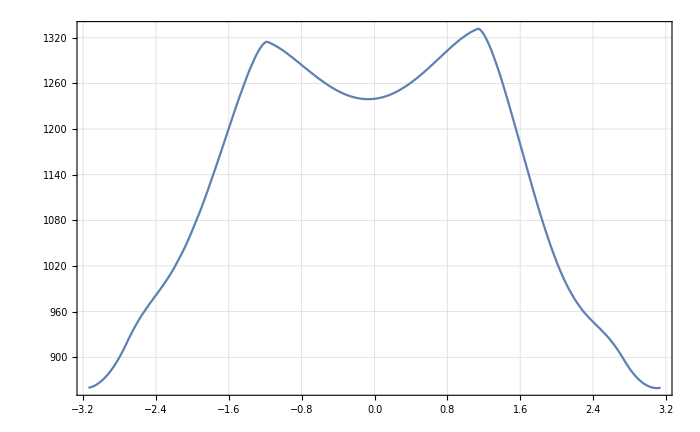

```mathematica
Plot[Int2DwNBeamCompiledManualphiAAllLimitspLimitsXManualInt[0.,{{0.,0.}},{phiDet,Pi/4},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4][[1]],{phiDet,-Pi,Pi},PlotPoints->10]
```

### 1994s

```mathematica
ManualphiAIntegrandAllLimits[0.,0.,0.,{-3,Pi,0.09,π/4},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False]
```

0.

```mathematica
Table[
NIntegrate[
ManualphiAIntegrandAllLimits[0,{{0,0}}[[bin,2]],{{0,0}}[[bin,1]],{phiDV,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False],(*{th0,0.,thetamax[rF]},{phiDet,-Pi//N,Pi//N},*)
{
p,
0.,
Sequence@@pLimitsApertXList[{{0,0}}[[bin,2]],{{0,0}}[[bin,1]],Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],
pmax
},
{phiDV,-Pi//N,Pi//N},PrecisionGoal->4,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10],
{bin,1,Length[{{0,0}}]}]
```

{859.713}

```mathematica
Table[i,{i,1,1}]
```

{1}

## First Fit try

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeamdB=
Table[Table[{bin,FitFuncBinwNbeam[bin,b,XYDatam05p75XOffset,{Pi//N,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}],
{b,{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```